```mathematica
A=({{-4, -1, -4/3}, {0, -2, 8/3}, {1, -1, -6}})
```

{{-4,-1,-4/3},{0,-2,8/3},{1,-1,-6}}

Determino gli autovalori di A

```mathematica
λ=Eigenvalues[A]
```

{-4,-4,-4}

Analizzo il polinomio minimo

```mathematica
Simplify[ResourceFunction["MatrixMinimalPolynomial"][A,x]]
```

(4+x)^3

Analizzo il grafico dei modi polinomial-esponenziali

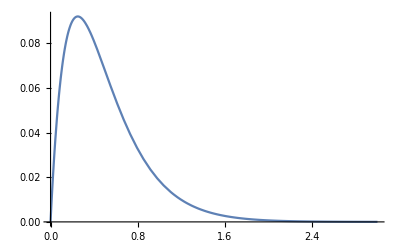

```mathematica
Plot[t Exp[-4 t],{t,0,3},PlotRange->All]
```

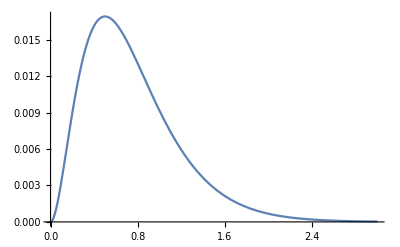

```mathematica
Plot[t^2/2 Exp[-4 t],{t,0,3},PlotRange->All]
```